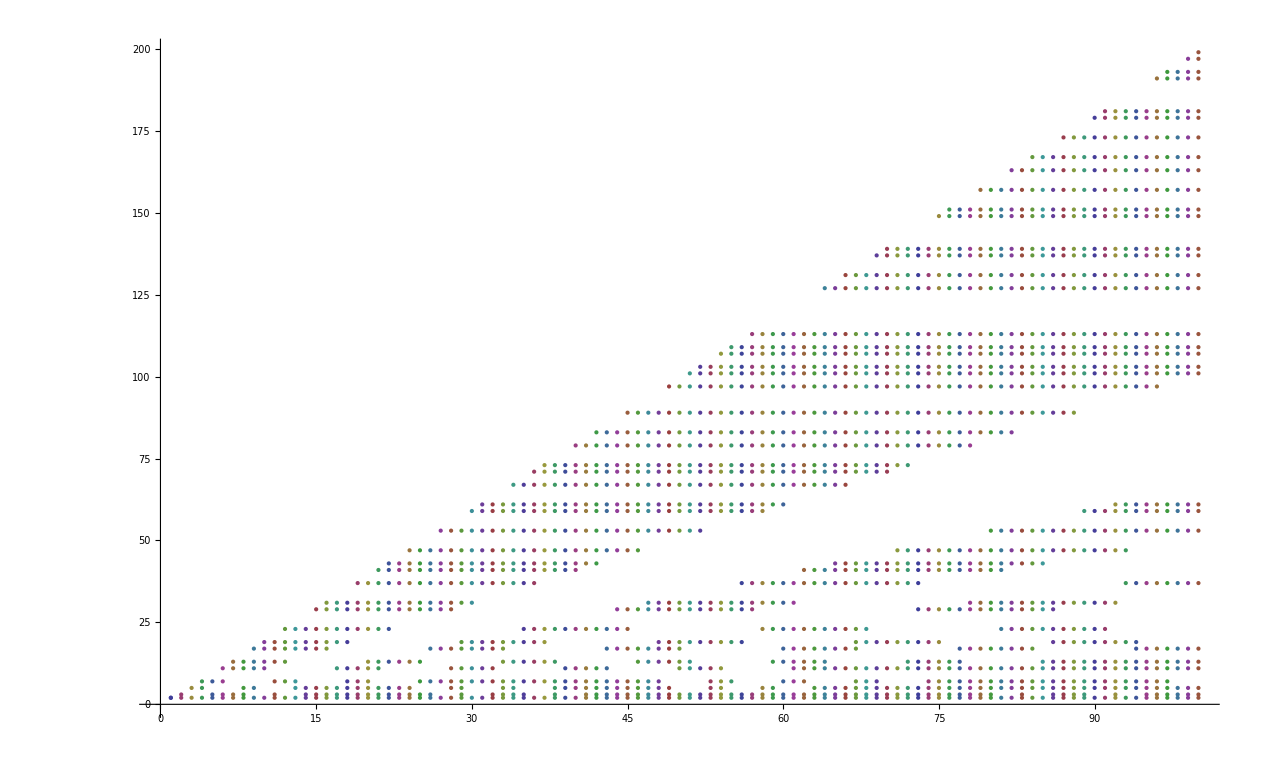

```mathematica
ListPlot[Table[{n,p},{n,1,100},{p,Table[x[[1]],{x,FactorInteger[Binomial[2 n,n]]}]}],ImageSize->Large, ColorFunctionScaling->False, PlotStyle->Directive[ColorFunction->Function[{x,y},If[EisenSteinQ[y], Red, Black]]]]
```

```mathematica
EisenSteinQ[p_] := Mod[p,3] == 2;
```